```mathematica
p = 36.9983017*10^5; 
W = (0.661813625)*10^-6;
T= 320.50709792;
R=  8.3145;
a= 0.7857;
b=0.08786*10^(-3);
ν=0.0017768323063151684;
ν2=0.00245026;
T30=302.75;
a2=0.8097474323916911;
b2=0.00009003306041125126;
```

```mathematica
Solve[(p+(v^2*a2)/W^2)(W-v*b2)== v*R*T,{v}]
```

{{v→0.00245026},{v→0.00245026},{v→0.00245026}}

```mathematica
(27*R^2*T^2)/(64*p)
```

0.809747

```mathematica
W/(3b2)
```

0.00245026

```mathematica
(R*T)/(8*p)
```

0.0000900331

```mathematica
(ν2*R*T)/(p*W)
```

2.66667

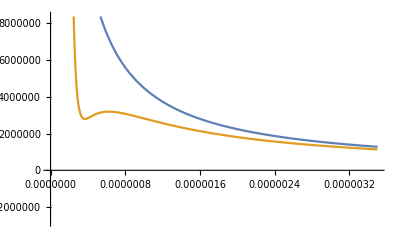

```mathematica
Plot[{(ν*R*T30)/V,(ν*R*T30)/(V-ν*b)-(ν^2*a)/V^2},{V,0,3.5*10^-6}]
```

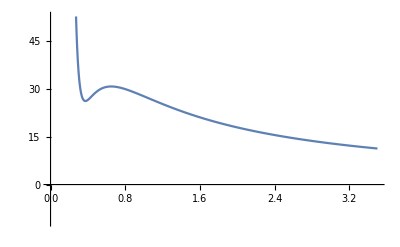

```mathematica
Plot[(0.00177683*8.3145*10^(-5)*302.75)/(x*10^(-6)-0.00177683*0.0000900331)-(0.00177683^2*8.09747*10^(-6))/((x*10^(-6))^2),{x,0,3.5}]
```

```mathematica
1/(3 b2)*0.03*10^-6
```

0.00011107

```mathematica
√(((27 R^2 T)/(32p)*0.749)^2+((27 R^2 T^2)/(64 p^2)*0.6)^2)
```

0.00378463

```mathematica
√((R/(8p)*0.749)^2+((R T)/(8 p^2)*0.6)^2)
```

2.104×10^-7

```mathematica
√(((ν R)/(p W)*0.749)^2+((ν R T)/(p^2 W)*0.6)^2+((ν R T)/(p W^2)*0.06*10^-6)^2+((R T)/(p W)*0.00039))
```

0.674685